# Concatenated Dynamic Decoupling Performance

#### Parameter Dependencies

```mathematica
(*Standard Units*)
planck = 6.626 10^-34;
planckred = 1 10^-34
(*Pauli Matrices*)
x={{0,1},{1,0}};
xdd = KroneckerProduct[x, IdentityMatrix[2]];
MatrixForm[x]
MatrixForm[xdd]
y={{I,0},{0,-I}};
ydd = KroneckerProduct[y, IdentityMatrix[2]];
MatrixForm[y]
MatrixForm[ydd]
z={{1,0},{0,-1}};
zdd =KroneckerProduct[z, IdentityMatrix[2]];
MatrixForm[z]
MatrixForm[zdd]
paulilist = {x,y,z};
```

1/10000000000000000000000000000000000

(0 | 1
1 | 0)

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

(ⅈ | 0
0 | -ⅈ)

(ⅈ | 0 | 0 | 0
0 | ⅈ | 0 | 0
0 | 0 | -ⅈ | 0
0 | 0 | 0 | -ⅈ)

(1 | 0
0 | -1)

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

#### Function Definitions

```mathematica
(*Setting up Parameter and Function Values *)
ClearAll[SBHamiltonian,BathHamiltonian,PartZ,Sq,Bq,State,divtest,FreqF, Mmax, FreeEvolutionInterval, ft, XY4, Fidelity]
(*Bath Hamiltonian*)
BathHamiltonian[w_] := w z
(*System-Bath Hamiltonian*)
SBHamiltonian[l1_, l2_] := Sum[KroneckerProduct[Extract[l1, i], Extract[l2, i]], {i,1,3}]
(*Partition Function*)
PartZ[b_, w_] := Tr[N[MatrixExp[-b BathHamiltonian[w]]]]
(*quantum state*)
Sq = Outer[Times, 1/Sqrt[2] {1,1}, 1/Sqrt[2] {1,1}];
(*bath state*)
Bq[b_, w_] := MatrixExp[-b BathHamiltonian[w]] / PartZ[b, w]
(*Total State*)
State[b_, w_] := KroneckerProduct[Sq, Bq[b,w]]
(*energy for frequency value*)
FreqF[c_] := Divide[c 1.6 10^-19, planck]; (*Joules*)
(*tau value*)
FreeEvolutionInterval[T_, m_]:= N[Divide[T, 4^m]]
(*Free Evolution Sequence*)
ft[t_, totham_] := MatrixExp[-I t totham];

(*Concatenated Dynamic Decoupling Recursion*)
XY4[m_]  := XY4[m] = N[zdd.XY4[m-1].xdd.XY4[m-1].zdd.XY4[m-1].xdd.XY4[m-1]];
(*List of m Unitaries*)
SetAttributes[{Moperators,Evolvedstates,Tracedstates,Fidelitylist}, HoldFirst];
Moperators[l_,m_] := Do[AppendTo[l, XY4[x]], {x, 0, m}];
(*Table of Final State at each concatenation interval*)
Evolvedstates[out_,op_,in_] := Do[AppendTo[out, Extract[op, x].in.ConjugateTranspose[Extract[op, x]]], {x,Length[op]}];
(*Table of Final States over time interval*)
Evolvedstatestime[in_,uni_, t_] := NestList[uni.#.ConjugateTranspose[uni]&, in,t];
(*Table of Traced Final System States at each concatenation interval*)
Tracedstates[trl_, st_] := Do[AppendTo[trl, ResourceFunction["MatrixPartialTrace"][Extract[st,x],1,2]], {x, 1, Length[st]}];
(*Uhlman fidelity*)
Fidelity[p_, f_] := Tr[MatrixPower[MatrixPower[p, 1/2].f.MatrixPower[p, 1/2], 1/2]]^2;
(*Tr[MatrixPower[MatrixPower[f, 1/2].p.MatrixPower[f, 1/2], 1/2]]^2/(Tr[f]*Tr[p])*)
(*Table of Fidelities at each concatenation interval*)
Fidelitylist[l1_, in_, l2_] := Do[AppendTo[l1, N[Fidelity[in, Extract[l2,x]]]], {x,1, Length[l2]}];
```

#### Generate System-Bath Hamiltonian and System-Bath Operators

H_sb=∑_(i={X, Y,  Z})^3 σ_i⊗B_i]
SBHamiltonian[{X,Y,Z}, {X,Y_,Z}] := Sum[KroneckerProduct[Extract[l1, i], Extract[l2, i]], {i,1,3}]

```mathematica
ClearAll[sigmalist, paulilist]
sigmalist = {};
paulilist = {x,y,z};
(*System-bath Hamiltonian Bath Unitaries 
Do[AppendTo[sigmalist, RandomVariate[CircularUnitaryMatrixDistribution[2]]], 3];
Print["System-Bath Unitaries are"]
Do[Print[MatrixForm[Extract[sigmalist,i]]], {i,1,3}] *)
(*System-bath Hamiltonian*)
Print["System-Bath Hamiltonian is"]
MatrixForm[SBham = SBHamiltonian[paulilist, paulilist]]
(*Check Hermatian?*)
Print["SBHam Hermatian?"]
SBham == ConjugateTranspose[SBham]
```

System-Bath Hamiltonian is

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

SBHam Hermatian?

True

#### Set Parameter Values

From Page 143 of Textbook and Problem 2
J  = ‖H_SB‖
 B = ‖H_B‖
 w = E/ℏ
 t  = T/4^m, initially T/4

```mathematica
Print["Energy (J) is(coupling strength)"]
j =  1 (*---FreqF[.005]---Norm[SBham, 2]*)
JSBham = j SBham;
Print["System-Bath Hamiltonian is"]
MatrixForm[JSBham]
Print["Frequency (w) of Bath is"]
(*-----------Set Hamiltonian Frequency-----------*)
w = .5 (*---FreqF[.005]---*)
Print["Bath Hamiltonian is"]
MatrixForm[BathHam = BathHamiltonian[w]]
Print["Check if Bath Hamiltonian is Hermatian"]
BathHam == ConjugateTranspose[BathHam]
Print["Inverse Temperature (B) is "] 
b = 1 (*Norm[BathHam, 2]*)
(*-----------Set Concatenation Level-----------*)
Print["The Concatenation Level is"]
m = 30
(*-----------Set Free Evolution Interval-----------*)
Print["Free Evolution Interval (t) (parameterized by T, m) is"]
t = .001 (*FreeEvolutionInterval[1, 1]*)
```

Energy (J) is(coupling strength)

1

System-Bath Hamiltonian is

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

Frequency (w) of Bath is

0.5

Bath Hamiltonian is

(0.5 | 0.
0. | -0.5)

Check if Bath Hamiltonian is Hermatian

True

Inverse Temperature (B) is

1

The Concatenation Level is

30

Free Evolution Interval (t) (parameterized by T, m) is

0.001

#### Concatenated Dynamic Decoupling Operators for m Levels

CDD=Z(U_(m-1)(T_(m-1)))XU_(m-1)(T_(m-1)))ZU_(m-1)(T_(m-1)))XU_(m-1)(T_(m-1)))
CDD_o=e^(it(H_sb+H_(b)))=U_0(T_o)

(*Free Evolution Sequence*)
ft[t_, totham_] := MatrixExp[-I t totham];

(*Concatenated Dynamic Decoupling Recursion*)
XY4[m_]  := XY4[m] = zdd.XY4[m-1].xdd.XY4[m-1].zdd.XY4[m-1].xdd.XY4[m-1];

(*List of m Unitaries*)
Moperators[l_,m_, start_] := Do[AppendTo[l, XY4[x]], {x, start, m}];

```mathematica
ClearAll[cddop]
cddop = {};
Print["The Total Hamiltonian is"]
MatrixForm[totalhamiltonian = JSBham + KroneckerProduct[IdentityMatrix[2], BathHam]]
MatrixForm[N[MatrixExp[-I t totalhamiltonian]]]
Print["Check if total hamiltonian is Hermatian?"]
totalhamiltonian == ConjugateTranspose[totalhamiltonian]
Print["Check if exp^(total hamiltonian) is Unitary?"]
MatrixForm[N[MatrixExp[-I totalhamiltonian].ConjugateTranspose[MatrixExp[-I totalhamiltonian]]]]
Print["The Initial Operator XY4[t_0]=(e^itH) is"]
XY4[0] = ft[t, totalhamiltonian];
MatrixForm[XY4[0]]
Moperators[cddop, m]
Print["The Final M operator is"]
MatrixForm[Extract[cddop, m]]
Print["Check if total final hamiltonian is Hermatian?"]
Extract[cddop, m] == ConjugateTranspose[Extract[cddop, m]]
Print["Check if total final hamiltonian is Unitary?"]
MatrixForm[Extract[cddop, m].ConjugateTranspose[Extract[cddop, m]]]
```

The Total Hamiltonian is

(0.5 | 0. | 0. | 1.
0. | -0.5 | 1. | 0.
0. | 1. | 0.5 | 0.
1. | 0. | 0. | -0.5)

(0.999999-0.0005 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -9.4143×10^-24-0.001 ⅈ
0.+0. ⅈ | 0.999999+0.0005 ⅈ | 9.4143×10^-24-0.001 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.0737×10^-23-0.001 ⅈ | 0.999999-0.0005 ⅈ | 0.+0. ⅈ
-1.0737×10^-23-0.001 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.999999+0.0005 ⅈ)

Check if total hamiltonian is Hermatian?

True

Check if exp^(total hamiltonian) is Unitary?

(1.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -5.55112×10^-17+0. ⅈ
0.+0. ⅈ | 1.+0. ⅈ | 5.55112×10^-17+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 5.55112×10^-17+0. ⅈ | 1.+0. ⅈ | 0.+0. ⅈ
-5.55112×10^-17+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.+0. ⅈ)

The Initial Operator XY4[t_0]=(e^itH) is

(0.999999-0.0005 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -9.4143×10^-24-0.001 ⅈ
0.+0. ⅈ | 0.999999+0.0005 ⅈ | 9.4143×10^-24-0.001 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.0737×10^-23-0.001 ⅈ | 0.999999-0.0005 ⅈ | 0.+0. ⅈ
-1.0737×10^-23-0.001 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.999999+0.0005 ⅈ)

The Final M operator is

(319568.+11428.5 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.15598-7.48707×10^-15 ⅈ
0.+0. ⅈ | 319568.-11428.5 ⅈ | -0.15598-7.48707×10^-15 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.15598-7.48707×10^-15 ⅈ | 319568.+11428.5 ⅈ | 0.+0. ⅈ
-0.15598-7.48707×10^-15 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 319568.-11428.5 ⅈ)

Check if total final hamiltonian is Hermatian?

False

Check if total final hamiltonian is Unitary?

(1.02254×10^11+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.02254×10^11+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 1.02254×10^11+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 1.02254×10^11+0. ⅈ)

#### Create Initial State

```mathematica
Print["The Partition Value is"]
part = PartZ[b,w]
Print["The Initial System Quibit is"]
MatrixForm[Sq]
Print["The Bath System Quibit is"]
bathq = Bq[b,w];
MatrixForm[bathq]
Print["The Total State Initial is"]
initialstate = State[b,w];
MatrixForm[initialstate]
```

The Partition Value is

2.25525

The Initial System Quibit is

(1/2 | 1/2
1/2 | 1/2)

The Bath System Quibit is

(0.268941 | 0.
0. | 0.731059)

The Total State Initial is

(0.134471 | 0. | 0.134471 | 0.
0. | 0.365529 | 0. | 0.365529
0.134471 | 0. | 0.134471 | 0.
0. | 0.365529 | 0. | 0.365529)

#### Evolved State at each Concatenation Level

U_m(T_m)=Z(U_(m-1)(T_(m-1)))XU_(m-1)(T_(m-1)))ZU_(m-1)(T_(m-1)))XU_(m-1)(T_(m-1)))
p_m=U_m(T_m)p_o(U_m(T_m))^(*T)

List of Final States at each concatenation interval
Evolvedstates[out_,op_,in_, start_] := Do[AppendTo[out, Extract[op, x].in.ConjugateTranspose[Extract[op, x]]], {x,1,Length[op]}];

```mathematica
(*allfinal = Table[{m, operators[]}, {m, 1, 20}] //TableForm*)
ClearAll[finalout]
finalout ={};
Evolvedstates[finalout, cddop, initialstate]//Chop
MatrixForm[XY4[0]]
Do[Print[MatrixForm[Extract[finalout, x]]],{x,1,m}]
```

(0.999999-0.0005 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -9.4143×10^-24-0.001 ⅈ
0.+0. ⅈ | 0.999999+0.0005 ⅈ | 9.4143×10^-24-0.001 ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 1.0737×10^-23-0.001 ⅈ | 0.999999-0.0005 ⅈ | 0.+0. ⅈ
-1.0737×10^-23-0.001 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.999999+0.0005 ⅈ)

(0.134471+1.35525×10^-20 ⅈ | -1.15529×10^-7-0.000231058 ⅈ | 0.134471-7.36591×10^-27 ⅈ | -1.15529×10^-7-0.000231058 ⅈ
-1.15529×10^-7+0.000231058 ⅈ | 0.365529+0. ⅈ | -1.15529×10^-7+0.000231058 ⅈ | 0.365529+2.70977×10^-27 ⅈ
0.134471+1.35525×10^-20 ⅈ | -1.15529×10^-7-0.000231058 ⅈ | 0.134471+0. ⅈ | -1.15529×10^-7-0.000231058 ⅈ
-1.15529×10^-7+0.000231058 ⅈ | 0.365529-2.70977×10^-27 ⅈ | -1.15529×10^-7+0.000231058 ⅈ | 0.365529+0. ⅈ)

(0.134471+0. ⅈ | -9.24231×10^-7+1.84846×10^-9 ⅈ | 0.134471+6.34091×10^-25 ⅈ | -9.24231×10^-7+1.84846×10^-9 ⅈ
-9.24231×10^-7-1.84846×10^-9 ⅈ | 0.365529-1.0842×10^-19 ⅈ | -9.24231×10^-7-1.84846×10^-9 ⅈ | 0.365529-1.0842×10^-19 ⅈ
0.134471-6.34091×10^-25 ⅈ | -9.24231×10^-7+1.84846×10^-9 ⅈ | 0.134471+0. ⅈ | -9.24231×10^-7+1.84846×10^-9 ⅈ
-9.24231×10^-7-1.84846×10^-9 ⅈ | 0.365529-1.0842×10^-19 ⅈ | -9.24231×10^-7-1.84846×10^-9 ⅈ | 0.365529-1.0842×10^-19 ⅈ)

(0.134471+0. ⅈ | 1.18299×10^-10+1.47871×10^-8 ⅈ | 0.134471+7.92608×10^-29 ⅈ | 1.18299×10^-10+1.47871×10^-8 ⅈ
1.18299×10^-10-1.47871×10^-8 ⅈ | 0.365529+0. ⅈ | 1.18299×10^-10-1.47871×10^-8 ⅈ | 0.365529-2.91584×10^-29 ⅈ
0.134471-7.92608×10^-29 ⅈ | 1.18299×10^-10+1.47871×10^-8 ⅈ | 0.134471+2.24208×10^-44 ⅈ | 1.18299×10^-10+1.47871×10^-8 ⅈ
1.18299×10^-10-1.47871×10^-8 ⅈ | 0.365529+2.91584×10^-29 ⅈ | 1.18299×10^-10-1.47871×10^-8 ⅈ | 0.365529-5.60519×10^-45 ⅈ)

(0.134471+0. ⅈ | 9.4585×10^-10-3.02774×10^-11 ⅈ | 0.134471+1.58509×10^-31 ⅈ | 9.4585×10^-10-3.02774×10^-11 ⅈ
9.4585×10^-10+3.02774×10^-11 ⅈ | 0.365529+1.09476×10^-47 ⅈ | 9.4585×10^-10+3.02774×10^-11 ⅈ | 0.365529-5.83123×10^-32 ⅈ
0.134471-1.58509×10^-31 ⅈ | 9.4585×10^-10-3.02774×10^-11 ⅈ | 0.134471+0. ⅈ | 9.4585×10^-10-3.02774×10^-11 ⅈ
9.4585×10^-10+3.02774×10^-11 ⅈ | 0.365529+5.83123×10^-32 ⅈ | 9.4585×10^-10+3.02774×10^-11 ⅈ | 0.365529+0. ⅈ)

(0.134471+0. ⅈ | -3.08878×10^-11-2.39992×10^-10 ⅈ | 0.134471+5.06623×10^-33 ⅈ | -3.08878×10^-11-2.39992×10^-10 ⅈ
-3.08878×10^-11+2.39992×10^-10 ⅈ | 0.365529+6.93889×10^-18 ⅈ | -3.08878×10^-11+2.39992×10^-10 ⅈ | 0.365529+6.93889×10^-18 ⅈ
0.134471-5.06623×10^-33 ⅈ | -3.08878×10^-11-2.39992×10^-10 ⅈ | 0.134471-2.73691×10^-48 ⅈ | -3.08878×10^-11-2.39992×10^-10 ⅈ
-3.08878×10^-11+2.39992×10^-10 ⅈ | 0.365529+6.93889×10^-18 ⅈ | -3.08878×10^-11+2.39992×10^-10 ⅈ | 0.365529+6.93889×10^-18 ⅈ)

(0.134471+6.93889×10^-18 ⅈ | -2.11905×10^-10+1.19088×10^-10 ⅈ | 0.134471+6.93889×10^-18 ⅈ | -2.11905×10^-10+1.19088×10^-10 ⅈ
-2.11905×10^-10-1.19088×10^-10 ⅈ | 0.365529-2.77556×10^-17 ⅈ | -2.11905×10^-10-1.19088×10^-10 ⅈ | 0.365529-2.77556×10^-17 ⅈ
0.134471+6.93889×10^-18 ⅈ | -2.11905×10^-10+1.19088×10^-10 ⅈ | 0.134471+6.93889×10^-18 ⅈ | -2.11905×10^-10+1.19088×10^-10 ⅈ
-2.11905×10^-10-1.19088×10^-10 ⅈ | 0.365529-2.77556×10^-17 ⅈ | -2.11905×10^-10-1.19088×10^-10 ⅈ | 0.365529-2.77556×10^-17 ⅈ)

(0.134471+0. ⅈ | 6.43148×10^-10-3.32543×10^-10 ⅈ | 0.134471+7.69807×10^-33 ⅈ | 6.43148×10^-10-3.32543×10^-10 ⅈ
6.43148×10^-10+3.32543×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ | 6.43148×10^-10+3.32543×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ
0.134471-7.69807×10^-33 ⅈ | 6.43148×10^-10-3.32543×10^-10 ⅈ | 0.134471-2.18953×10^-47 ⅈ | 6.43148×10^-10-3.32543×10^-10 ⅈ
6.43148×10^-10+3.32543×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ | 6.43148×10^-10+3.32543×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ)

(0.134471-6.93889×10^-18 ⅈ | -3.59907×10^-10-1.02396×10^-9 ⅈ | 0.134471-6.93889×10^-18 ⅈ | -3.59907×10^-10-1.02396×10^-9 ⅈ
-3.59907×10^-10+1.02396×10^-9 ⅈ | 0.365529+2.18953×10^-47 ⅈ | -3.59907×10^-10+1.02396×10^-9 ⅈ | 0.365529+8.09872×10^-33 ⅈ
0.134471-6.93889×10^-18 ⅈ | -3.59907×10^-10-1.02396×10^-9 ⅈ | 0.134471-6.93889×10^-18 ⅈ | -3.59907×10^-10-1.02396×10^-9 ⅈ
-3.59907×10^-10+1.02396×10^-9 ⅈ | 0.365529-8.09872×10^-33 ⅈ | -3.59907×10^-10+1.02396×10^-9 ⅈ | 0.365529+2.18953×10^-47 ⅈ)

(0.134471+0. ⅈ | -8.79259×10^-10-1.95521×10^-10 ⅈ | 0.134471+5.30408×10^-32 ⅈ | -8.79259×10^-10-1.95521×10^-10 ⅈ
-8.79259×10^-10+1.95521×10^-10 ⅈ | 0.365529+0. ⅈ | -8.79259×10^-10+1.95521×10^-10 ⅈ | 0.365529-1.95126×10^-32 ⅈ
0.134471-5.30408×10^-32 ⅈ | -8.79259×10^-10-1.95521×10^-10 ⅈ | 0.134471+4.37906×10^-47 ⅈ | -8.79259×10^-10-1.95521×10^-10 ⅈ
-8.79259×10^-10+1.95521×10^-10 ⅈ | 0.365529+1.95126×10^-32 ⅈ | -8.79259×10^-10+1.95521×10^-10 ⅈ | 0.365529-2.18953×10^-47 ⅈ)

(0.134471+1.09476×10^-47 ⅈ | -2.12388×10^-10-2.54443×10^-10 ⅈ | 0.134471-6.91769×10^-32 ⅈ | -2.12388×10^-10-2.54443×10^-10 ⅈ
-2.12388×10^-10+2.54443×10^-10 ⅈ | 0.365529+0. ⅈ | -2.12388×10^-10+2.54443×10^-10 ⅈ | 0.365529+2.54487×10^-32 ⅈ
0.134471+6.91769×10^-32 ⅈ | -2.12388×10^-10-2.54443×10^-10 ⅈ | 0.134471-3.42114×10^-49 ⅈ | -2.12388×10^-10-2.54443×10^-10 ⅈ
-2.12388×10^-10+2.54443×10^-10 ⅈ | 0.365529-2.54487×10^-32 ⅈ | -2.12388×10^-10+2.54443×10^-10 ⅈ | 0.365529+8.55285×10^-50 ⅈ)

(0.134471+0. ⅈ | -2.93965×10^-10+7.82478×10^-10 ⅈ | 0.134471+9.57083×10^-32 ⅈ | -2.93965×10^-10+7.82478×10^-10 ⅈ
-2.93965×10^-10-7.82478×10^-10 ⅈ | 0.365529-1.38778×10^-17 ⅈ | -2.93965×10^-10-7.82478×10^-10 ⅈ | 0.365529-1.38778×10^-17 ⅈ
0.134471-9.57083×10^-32 ⅈ | -2.93965×10^-10+7.82478×10^-10 ⅈ | 0.134471+0. ⅈ | -2.93965×10^-10+7.82478×10^-10 ⅈ
-2.93965×10^-10-7.82478×10^-10 ⅈ | 0.365529-1.38778×10^-17 ⅈ | -2.93965×10^-10-7.82478×10^-10 ⅈ | 0.365529-1.38778×10^-17 ⅈ)

(0.134471-1.75162×10^-46 ⅈ | -2.73922×10^-10-2.04257×10^-9 ⅈ | 0.134471+2.50802×10^-31 ⅈ | -2.73922×10^-10-2.04257×10^-9 ⅈ
-2.73922×10^-10+2.04257×10^-9 ⅈ | 0.365529-8.75812×10^-47 ⅈ | -2.73922×10^-10+2.04257×10^-9 ⅈ | 0.365529-9.22648×10^-32 ⅈ
0.134471-2.50802×10^-31 ⅈ | -2.73922×10^-10-2.04257×10^-9 ⅈ | 0.134471-1.75162×10^-46 ⅈ | -2.73922×10^-10-2.04257×10^-9 ⅈ
-2.73922×10^-10+2.04257×10^-9 ⅈ | 0.365529+9.22648×10^-32 ⅈ | -2.73922×10^-10+2.04257×10^-9 ⅈ | 0.365529+0. ⅈ)

(0.134471+0. ⅈ | -1.46748×10^-10-2.48606×10^-10 ⅈ | 0.134471-1.34297×10^-31 ⅈ | -1.46748×10^-10-2.48606×10^-10 ⅈ
-1.46748×10^-10+2.48606×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ | -1.46748×10^-10+2.48606×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ
0.134471+1.34297×10^-31 ⅈ | -1.46748×10^-10-2.48606×10^-10 ⅈ | 0.134471+0. ⅈ | -1.46748×10^-10-2.48606×10^-10 ⅈ
-1.46748×10^-10+2.48606×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ | -1.46748×10^-10+2.48606×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ)

(0.134471+0. ⅈ | 4.64074×10^-10+7.36631×10^-10 ⅈ | 0.134471-3.97726×10^-31 ⅈ | 4.64074×10^-10+7.36631×10^-10 ⅈ
4.64074×10^-10-7.36631×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ | 4.64074×10^-10-7.36631×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ
0.134471+3.97726×10^-31 ⅈ | 4.64074×10^-10+7.36631×10^-10 ⅈ | 0.134471+0. ⅈ | 4.64074×10^-10+7.36631×10^-10 ⅈ
4.64074×10^-10-7.36631×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ | 4.64074×10^-10-7.36631×10^-10 ⅈ | 0.365529+2.77556×10^-17 ⅈ)

(0.134471-1.38778×10^-17 ⅈ | 1.30411×10^-9-1.05014×10^-9 ⅈ | 0.134471-1.38778×10^-17 ⅈ | 1.30411×10^-9-1.05014×10^-9 ⅈ
1.30411×10^-9+1.05014×10^-9 ⅈ | 0.365529+0. ⅈ | 1.30411×10^-9+1.05014×10^-9 ⅈ | 0.365529-4.11081×10^-31 ⅈ
0.134471-1.38778×10^-17 ⅈ | 1.30411×10^-9-1.05014×10^-9 ⅈ | 0.134471-1.38778×10^-17 ⅈ | 1.30411×10^-9-1.05014×10^-9 ⅈ
1.30411×10^-9+1.05014×10^-9 ⅈ | 0.365529+4.11081×10^-31 ⅈ | 1.30411×10^-9+1.05014×10^-9 ⅈ | 0.365529+0. ⅈ)

(0.134471+0. ⅈ | -3.73061×10^-9-1.71023×10^-9 ⅈ | 0.134471-1.82591×10^-30 ⅈ | -3.73061×10^-9-1.71023×10^-9 ⅈ
-3.73061×10^-9+1.71023×10^-9 ⅈ | 0.365529+2.77556×10^-17 ⅈ | -3.73061×10^-9+1.71023×10^-9 ⅈ | 0.365529+2.77556×10^-17 ⅈ
0.134471+1.82591×10^-30 ⅈ | -3.73061×10^-9-1.71023×10^-9 ⅈ | 0.134471+0. ⅈ | -3.73061×10^-9-1.71023×10^-9 ⅈ
-3.73061×10^-9+1.71023×10^-9 ⅈ | 0.365529+2.77556×10^-17 ⅈ | -3.73061×10^-9+1.71023×10^-9 ⅈ | 0.365529+2.77556×10^-17 ⅈ)

(0.134471-5.60519×10^-45 ⅈ | 1.11812×10^-8+1.67359×10^-9 ⅈ | 0.134471-5.47398×10^-30 ⅈ | 1.11812×10^-8+1.67359×10^-9 ⅈ
1.11812×10^-8-1.67359×10^-9 ⅈ | 0.365529+0. ⅈ | 1.11812×10^-8-1.67359×10^-9 ⅈ | 0.365529+2.01376×10^-30 ⅈ
0.134471+5.47398×10^-30 ⅈ | 1.11812×10^-8+1.67359×10^-9 ⅈ | 0.134471+0. ⅈ | 1.11812×10^-8+1.67359×10^-9 ⅈ
1.11812×10^-8-1.67359×10^-9 ⅈ | 0.365529-2.01376×10^-30 ⅈ | 1.11812×10^-8-1.67359×10^-9 ⅈ | 0.365529+0. ⅈ)

(0.134471+6.93889×10^-18 ⅈ | 1.62402×10^-9+1.09752×10^-9 ⅈ | 0.134471+6.93889×10^-18 ⅈ | 1.62402×10^-9+1.09752×10^-9 ⅈ
1.62402×10^-9-1.09752×10^-9 ⅈ | 0.36553-2.77556×10^-17 ⅈ | 1.62402×10^-9-1.09752×10^-9 ⅈ | 0.36553-2.77556×10^-17 ⅈ
0.134471+6.93889×10^-18 ⅈ | 1.62402×10^-9+1.09752×10^-9 ⅈ | 0.134471+6.93889×10^-18 ⅈ | 1.62402×10^-9+1.09752×10^-9 ⅈ
1.62402×10^-9-1.09752×10^-9 ⅈ | 0.36553-2.77556×10^-17 ⅈ | 1.62402×10^-9-1.09752×10^-9 ⅈ | 0.36553-2.77556×10^-17 ⅈ)

(0.134472+0. ⅈ | -4.17151×10^-9-4.35064×10^-9 ⅈ | 0.134472+9.20253×10^-30 ⅈ | -4.17151×10^-9-4.35064×10^-9 ⅈ
-4.17151×10^-9+4.35064×10^-9 ⅈ | 0.365531-2.77556×10^-17 ⅈ | -4.17151×10^-9+4.35064×10^-9 ⅈ | 0.365531-2.77556×10^-17 ⅈ
0.134472-9.20253×10^-30 ⅈ | -4.17151×10^-9-4.35064×10^-9 ⅈ | 0.134472+0. ⅈ | -4.17151×10^-9-4.35064×10^-9 ⅈ
-4.17151×10^-9+4.35064×10^-9 ⅈ | 0.365531-2.77556×10^-17 ⅈ | -4.17151×10^-9+4.35064×10^-9 ⅈ | 0.365531-2.77556×10^-17 ⅈ)

(0.134474+0. ⅈ | 1.73261×10^-8+1.45998×10^-9 ⅈ | 0.134474+2.82133×10^-30 ⅈ | 1.73261×10^-8+1.45998×10^-9 ⅈ
1.73261×10^-8-1.45998×10^-9 ⅈ | 0.365538+0. ⅈ | 1.73261×10^-8-1.45998×10^-9 ⅈ | 0.365538-1.03791×10^-30 ⅈ
0.134474-2.82133×10^-30 ⅈ | 1.73261×10^-8+1.45998×10^-9 ⅈ | 0.134474+0. ⅈ | 1.73261×10^-8+1.45998×10^-9 ⅈ
1.73261×10^-8-1.45998×10^-9 ⅈ | 0.365538+1.03791×10^-30 ⅈ | 1.73261×10^-8-1.45998×10^-9 ⅈ | 0.365538-5.60519×10^-45 ⅈ)

(0.134484+0. ⅈ | -3.82705×10^-9+1.09488×10^-8 ⅈ | 0.134484+0. ⅈ | -3.82705×10^-9+1.09488×10^-8 ⅈ
-3.82705×10^-9-1.09488×10^-8 ⅈ | 0.365565+0. ⅈ | -3.82705×10^-9-1.09488×10^-8 ⅈ | 0.365565+0. ⅈ
0.134484+0. ⅈ | -3.82705×10^-9+1.09488×10^-8 ⅈ | 0.134484+0. ⅈ | -3.82705×10^-9+1.09488×10^-8 ⅈ
-3.82705×10^-9-1.09488×10^-8 ⅈ | 0.365565+0. ⅈ | -3.82705×10^-9-1.09488×10^-8 ⅈ | 0.365565+0. ⅈ)

(0.134523-3.46945×10^-18 ⅈ | -6.1083×10^-9-2.65985×10^-8 ⅈ | 0.134523-3.46945×10^-18 ⅈ | -6.1083×10^-9-2.65985×10^-8 ⅈ
-6.1083×10^-9+2.65985×10^-8 ⅈ | 0.365671+0. ⅈ | -6.1083×10^-9+2.65985×10^-8 ⅈ | 0.365671+0. ⅈ
0.134523-3.46945×10^-18 ⅈ | -6.1083×10^-9-2.65985×10^-8 ⅈ | 0.134523-3.46945×10^-18 ⅈ | -6.1083×10^-9-2.65985×10^-8 ⅈ
-6.1083×10^-9+2.65985×10^-8 ⅈ | 0.365671+0. ⅈ | -6.1083×10^-9+2.65985×10^-8 ⅈ | 0.365671+0. ⅈ)

(0.134679+0. ⅈ | -8.37934×10^-9-6.60941×10^-9 ⅈ | 0.134679+0. ⅈ | -8.37934×10^-9-6.60941×10^-9 ⅈ
-8.37934×10^-9+6.60941×10^-9 ⅈ | 0.366095+0. ⅈ | -8.37934×10^-9+6.60941×10^-9 ⅈ | 0.366095+0. ⅈ
0.134679+0. ⅈ | -8.37934×10^-9-6.60941×10^-9 ⅈ | 0.134679+0. ⅈ | -8.37934×10^-9-6.60941×10^-9 ⅈ
-8.37934×10^-9+6.60941×10^-9 ⅈ | 0.366095+0. ⅈ | -8.37934×10^-9+6.60941×10^-9 ⅈ | 0.366095+0. ⅈ)

(0.135306-4.48416×10^-44 ⅈ | 2.30275×10^-8-1.17017×10^-8 ⅈ | 0.135306-4.48416×10^-44 ⅈ | 2.30275×10^-8-1.17017×10^-8 ⅈ
2.30275×10^-8+1.17017×10^-8 ⅈ | 0.367799+1.12104×10^-44 ⅈ | 2.30275×10^-8+1.17017×10^-8 ⅈ | 0.367799+1.12104×10^-44 ⅈ
0.135306-4.48416×10^-44 ⅈ | 2.30275×10^-8-1.17017×10^-8 ⅈ | 0.135306-4.48416×10^-44 ⅈ | 2.30275×10^-8-1.17017×10^-8 ⅈ
2.30275×10^-8+1.17017×10^-8 ⅈ | 0.367799+1.12104×10^-44 ⅈ | 2.30275×10^-8+1.17017×10^-8 ⅈ | 0.367799+1.12104×10^-44 ⅈ)

(0.137841+6.93889×10^-18 ⅈ | -7.21866×10^-8+2.31097×10^-8 ⅈ | 0.137841+6.93889×10^-18 ⅈ | -7.21866×10^-8+2.31097×10^-8 ⅈ
-7.21866×10^-8-2.31097×10^-8 ⅈ | 0.374691+0. ⅈ | -7.21866×10^-8-2.31097×10^-8 ⅈ | 0.374691+0. ⅈ
0.137841+6.93889×10^-18 ⅈ | -7.21866×10^-8+2.31097×10^-8 ⅈ | 0.137841+6.93889×10^-18 ⅈ | -7.21866×10^-8+2.31097×10^-8 ⅈ
-7.21866×10^-8-2.31097×10^-8 ⅈ | 0.374691+0. ⅈ | -7.21866×10^-8-2.31097×10^-8 ⅈ | 0.374691+0. ⅈ)

(0.148468+1.79366×10^-43 ⅈ | -1.88182×10^-8+5.46757×10^-8 ⅈ | 0.148468+1.79366×10^-43 ⅈ | -1.88182×10^-8+5.46757×10^-8 ⅈ
-1.88182×10^-8-5.46757×10^-8 ⅈ | 0.403579-1.38778×10^-17 ⅈ | -1.88182×10^-8-5.46757×10^-8 ⅈ | 0.403579-1.38778×10^-17 ⅈ
0.148468+1.79366×10^-43 ⅈ | -1.88182×10^-8+5.46757×10^-8 ⅈ | 0.148468+1.79366×10^-43 ⅈ | -1.88182×10^-8+5.46757×10^-8 ⅈ
-1.88182×10^-8-5.46757×10^-8 ⅈ | 0.403579-1.38778×10^-17 ⅈ | -1.88182×10^-8-5.46757×10^-8 ⅈ | 0.403579-1.38778×10^-17 ⅈ)

(0.199827+6.93889×10^-18 ⅈ | -6.04921×10^-8+1.51166×10^-8 ⅈ | 0.199827+6.93889×10^-18 ⅈ | -6.04921×10^-8+1.51166×10^-8 ⅈ
-6.04921×10^-8-1.51166×10^-8 ⅈ | 0.543186-2.77556×10^-17 ⅈ | -6.04921×10^-8-1.51166×10^-8 ⅈ | 0.543186-2.77556×10^-17 ⅈ
0.199827+6.93889×10^-18 ⅈ | -6.04921×10^-8+1.51166×10^-8 ⅈ | 0.199827+6.93889×10^-18 ⅈ | -6.04921×10^-8+1.51166×10^-8 ⅈ
-6.04921×10^-8-1.51166×10^-8 ⅈ | 0.543186-2.77556×10^-17 ⅈ | -6.04921×10^-8-1.51166×10^-8 ⅈ | 0.543186-2.77556×10^-17 ⅈ)

(0.655742+8.96831×10^-44 ⅈ | -5.20305×10^-8+7.74938×10^-8 ⅈ | 0.655742+8.96831×10^-44 ⅈ | -5.20305×10^-8+7.74938×10^-8 ⅈ
-5.20305×10^-8-7.74938×10^-8 ⅈ | 1.78249-4.48416×10^-44 ⅈ | -5.20305×10^-8-7.74938×10^-8 ⅈ | 1.78249-4.48416×10^-44 ⅈ
0.655742+8.96831×10^-44 ⅈ | -5.20305×10^-8+7.74938×10^-8 ⅈ | 0.655742+8.96831×10^-44 ⅈ | -5.20305×10^-8+7.74938×10^-8 ⅈ
-5.20305×10^-8-7.74938×10^-8 ⅈ | 1.78249-4.48416×10^-44 ⅈ | -5.20305×10^-8-7.74938×10^-8 ⅈ | 1.78249-4.48416×10^-44 ⅈ)

(76.0411+0. ⅈ | -0.0000156537-0.000015936 ⅈ | 76.0411+0. ⅈ | -0.0000156537-0.000015936 ⅈ
-0.0000156537+0.000015936 ⅈ | 206.701+2.29589×10^-41 ⅈ | -0.0000156537+0.000015936 ⅈ | 206.701+2.29589×10^-41 ⅈ
76.0411+0. ⅈ | -0.0000156537-0.000015936 ⅈ | 76.0411+0. ⅈ | -0.0000156537-0.000015936 ⅈ
-0.0000156537+0.000015936 ⅈ | 206.701+2.29589×10^-41 ⅈ | -0.0000156537+0.000015936 ⅈ | 206.701+2.29589×10^-41 ⅈ)

(1.37502×10^10-5.96046×10^-8 ⅈ | 11517.4+411.887 ⅈ | 1.37502×10^10-5.96046×10^-8 ⅈ | 11517.4+411.887 ⅈ
11517.4-411.887 ⅈ | 3.7377×10^10+0. ⅈ | 11517.4-411.887 ⅈ | 3.7377×10^10+0. ⅈ
1.37502×10^10-5.96046×10^-8 ⅈ | 11517.4+411.887 ⅈ | 1.37502×10^10-5.96046×10^-8 ⅈ | 11517.4+411.887 ⅈ
11517.4-411.887 ⅈ | 3.7377×10^10+0. ⅈ | 11517.4-411.887 ⅈ | 3.7377×10^10+0. ⅈ)

#### Fidelity of Evolved State at Each Concatenation Interval

ρ_m=U_m(T_m)ρ_0((U_m(T_m))^(t*)
𝐹(ρ_m, ρ_0)= tr[(√ρ_m ρ_0 √ρ_m)^(1/2)]^2

List of Final States at each concatenation interval
Evolvedstates[,op_,in_] := Do[AppendTo[out, Extract[op, x].in.ConjugateTranspose[Extract[op, x]]], {x,1,Length[op]}];

List of Traced Final System States at each concatenation interval
Tracedstates[trl_, st_] := Do[AppendTo[trl,ResourceFunction["MatrixPartialTrace"][Extract[st,x],1,2]], {x, 1, Length[st]}];

List of Fidelities at each concatenation interval
Fidelitylist[l1_, in_, l2_] := Do[AppendTo[l1, Fidelity[in, Extract[l2,x]]], {x,1, Length[l2]}];

Uhlman fidelity
Fidelity[p_, f_] := Tr[MatrixPower[MatrixPower[f, 1/2].p.MatrixPower[f, 1/2], 1/2]]^2/(Tr[f]*Tr[p])

ISSUE! Fidelity give complex values. For now, did Real[fidelity] to fix

```mathematica
ClearAll[finaltraced, fidelities]
finaltraced ={};
fidelities ={};
Print["The initial normalized partial system state is"]
MatrixForm[partialin = ResourceFunction["MatrixPartialTrace"][initialstate,1,2]]
Print["A final partial system state is"]
Tracedstates[finaltraced, finalout]
Fidelitylist[fidelities, partialin, finaltraced]
fixedfidelities = Re[fidelities] /. Indeterminate -> 0;
Print["The fidelities at each concatenation level are"]
fixedfidelities//TableForm
```

The initial normalized partial system state is

(0.268941 | 0.
0. | 0.731059)

A final partial system state is

The fidelities at each concatenation level are

1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.
1.00001
1.00002
1.0001
1.00039
1.00155
1.00621
1.02507
1.1041
1.48603
4.87647
565.484
1.02254×10^11
1.09327×10^44

#### Uhlman Fidelity at Each Concatenation Level up to m=20

```mathematica
Labeled[ListPlot[fixedfidelities,
  Joined -> True,
  PlotMarkers -> Graphics@{Disk[{0, 0}, Scaled@0.02]},
  AxesLabel -> {"m", "p"},
  PlotRange->{0,1},
  PlotLabel->"Ulhman Fidelity of System Qubit at each first Concatenated Pulse Sequence"],  
  {"Concatenation Level", "Ulhman Fidelity"}, 
  {Bottom, Left}, RotateLabel -> True]
```

-Graphics-Concatenation LevelUlhman Fidelity

#### Uhlman Fidelity over Time for each Concatenation Level

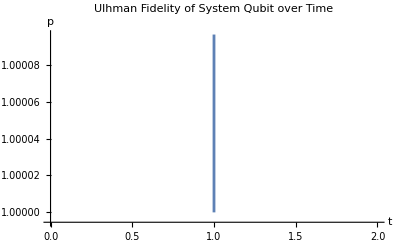
-Graphics-Time(T^4)Ulhman Fidelity

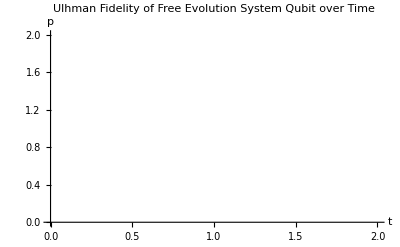
-Graphics-Time(T^4)Ulhman Fidelity

```mathematica
ClearAll[statesbycatlevel, finalout, fidelities, finaltraced, fixedfidelities, freeevolist,cddop]
statesbycatlevel = {};
finalout = {};
fidelities ={};
tracedout = {};
fixedfidelities ={};
statesovertimelist ={};
cddop = {};
T = 1;

(*create m concatenation levels*)
XY4[0] = ft[t, totalhamiltonian];
Moperators[cddop, 20]

(*Evolution Sequence*)
pos =1;
initialstate = State[b, w];
MatrixForm[initialstate];
tracedin = ResourceFunction["MatrixPartialTrace"][initialstate, 1,2];

While[pos<=Length[cddop],
statesovertimelist ={};
unitary = Extract[cddop, pos];
statesovertimelist = Evolvedstatestime[initialstate, unitary, T];
Tracedstates[tracedout, statesovertimelist];
Fidelitylist[fidelities, tracedin, tracedout];
fixedfidelities = Re[fidelities] /. Indeterminate -> 0;
AppendTo[statesbycatlevel,fixedfidelities];
finaltraced = {};
fidelities ={};
fixedfidelities ={};
tracedout = {};
pos= pos +5]

Labeled[ListPlot[statesbycatlevel,
Joined -> True,
PlotRange->All,
AxesLabel -> {"t", "p"},
PlotLegends->Automatic,
 PlotLabel->"Ulhman Fidelity of System Qubit over Time"],  
 {"Time(T^4)", "Ulhman Fidelity"},
 {Bottom, Left}, RotateLabel -> True]
 
 freeevolist ={};
 fixedfidelitiesfree ={};
 i=1;
 unitary =XY4[0];
 inistat= initialstate;
 While[i<=T,
 AppendTo[freeevolist, unitary.inistat.ConjugateTranspose[unitary]];
 inistat = Last[freeevolist];
 Tracedstates[tracedout, freeevolist];
Fidelitylist[fidelities, tracedin, tracedout];
fixedfidelitiesfree = Re[fidelities] /. Indeterminate -> 0;
finaltraced = {};
fidelities ={};
fixedfidelities ={};
tracedout = {};
 i++;
 ]

 
Labeled[ListPlot[fixedfidelitiesfree,
Joined -> True,
PlotRange->All,
AxesLabel -> {"t", "p"},
 PlotLabel->"Ulhman Fidelity of Free Evolution System Qubit over Time"],  
 {"Time(T^4)", "Ulhman Fidelity"}, 
 {Bottom, Left}, RotateLabel -> True]
```

## Analysis

We can see that for a fixed t, there is indeed an optimal CDD sequence at 6 from the first graph until it begins to fall off again. As we concatenate higher, the bath noise from the Hamiltonian gets pushed to higher orders and has less effect. The oscillating pattern is due to rabbi oscillations as if there is a finite system-bath size then there is no irreversible decay that will permanently place out state into the maximally mixed state (I.E purely classical). Without correcting, there is a natural oscillation cycle for the free evolution. The CDD sequence fights against these and should maintain a max error rate for a fixed t interval that we choose. We can see that the amplitude of oscillations becomes more narrow for higher m levels which is indicated by the more narrow fidelity min/max values.